```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITW20/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW20 Price | % Change | log return future | log return BITW20
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 68564.6 | 5.51% | 0.0212907 | 0.0536505
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 64983. | -25.14% | -0.0904653 | -0.289595
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 86809.9 | 0.97% | -0.0196938 | 0.00961259
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 85979.4 | 0.34% | -0.131645 | -0.042476
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 89710.1 | 14.05% | 0.03685 | 0.131487
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 78657. | -9.15% | -0.119603 | -0.0959278
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 86576.1 | -3.55% | -0.042369 | -0.0361124
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 89759.8 | 6.21% | 0.018947 | 0.0602416
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 84512.1 | -8.61% | -0.0359909 | -0.103831)

```mathematica
Dimensions[data]
```

{301,8}

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,8]]
```

log return BITW20

```mathematica
data[[1,7]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=80, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data =   
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,7;;8⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

80

79

78

77

76

75

74

73

72

71

70

69

68

67

66

65

64

63

62

61

60

59

58

57

56

55

54

53

52

51

50

49

48

47

46

45

44

43

42

41

40

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

General::munfl: 1.25331/(1.09180814843873×10^345) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NMinimize::nnum: The function value √((0.666667-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.666667-10. F2NIG2(«1»))^2+(0.466667-«19» («1»))^2+(0.333333-20. (-0.9+F2NIG2(«1»)))^2) is not a number at {α$586763035,β$586763035} = {28.2964,2.18771}.

20

NMinimize::nnum: The function value √((0.666667-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.666667-10. F2NIG2(«1»))^2+(0.466667-«19» («1»))^2+(0.4-20. (-0.9+F2NIG2(«1»)))^2) is not a number at {α$587208718,β$587208718} = {28.2964,2.18771}.

19

NMinimize::nnum: The function value √((0.666667-20. F2NIG2(InverseCDF[HyperbolicDistribution[«5»],0.05],«6»,InterpolatingFunction[{«1»},{«13»},{«1»},{«3»},{«1»}]))^2+(0.633333-10. F2NIG2(«1»))^2+(0.466667-«19» («1»))^2+(0.4-20. (-0.9+F2NIG2(«1»)))^2) is not a number at {α$587654481,β$587654481} = {28.2964,2.18771}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

18

17

16

15

14

13

12

11

10

9

8

7

6

5

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-366.687}. NIntegrate obtained 5248.65 and 66.0964 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-366.67}. NIntegrate obtained 5247.18 and 62.7113 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in z near {z} = {-366.645}. NIntegrate obtained 5277.86 and 90.1116 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

4

3

2

1

0

```mathematica
{α0,β0}
```

{2.00786,-0.26674}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_BITW20/

```mathematica
For[kk=0, kk≤80, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,8⟧;
rf=data2⟦2;;All,7⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.979888994160487}. NIntegrate obtained 0.0799749 and 0.000103272 for the integral and error estimates.

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.979888994160487}. NIntegrate obtained 0.0795443 and 0.000113264 for the integral and error estimates.

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.982732907728307}. NIntegrate obtained 0.0769185 and 0.000113122 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.542255 | 0.394283 | 0.354983 | 0.307302 | 0.296408 | 0.349975
 | 2021-05-13 | 0.544466 | 0.376974 | 0.38865 | 0.339415 | 0.329295 | 0.306206
 | 2021-05-06 | 0.541846 | 0.366616 | 0.344939 | 0.348813 | 0.317728 | 0.337198
 | 2021-04-29 | 0.553748 | 0.398914 | 0.355689 | 0.342486 | 0.320843 | 0.335444
 | 2021-04-22 | 0.547516 | 0.390511 | 0.386938 | 0.345949 | 0.317498 | 0.312121
 | 2021-04-15 | 0.539891 | 0.385201 | 0.382941 | 0.343866 | 0.31688 | 0.306925
 | 2021-04-08 | 0.538236 | 0.389048 | 0.346587 | 0.34109 | 0.31343 | 0.319482
 | 2021-04-01 | 0.555859 | 0.404696 | 0.358114 | 0.355186 | 0.327676 | 0.340397
 | 2021-03-25 | 0.551469 | 0.403874 | 0.347385 | 0.349991 | 0.320964 | 0.335614
 | 2021-03-18 | 0.550099 | 0.395263 | 0.381556 | 0.35149 | 0.32053 | 0.324929
 | 2021-03-11 | 0.552163 | 0.388958 | 0.369763 | 0.346706 | 0.323569 | 0.330654
 | 2021-03-04 | 0.572828 | 0.412882 | 0.354967 | 0.354016 | 0.334479 | 0.357222
 | 2021-02-25 | 0.561224 | 0.403257 | 0.346656 | 0.343326 | 0.32639 | 0.352695
 | 2021-02-18 | 0.553899 | 0.423054 | 0.34791 | 0.35584 | 0.310903 | 0.349048
 | 2021-02-10 | 0.554376 | 0.415935 | 0.355034 | 0.370256 | 0.314719 | 0.34023
 | 2021-02-03 | 0.592447 | 0.438363 | 0.410307 | 0.391388 | 0.345491 | 0.369587
 | 2021-01-27 | 0.600222 | 0.477343 | 0.365718 | 0.424587 | 0.363837 | 0.400157
 | 2021-01-20 | 0.592937 | 0.471418 | 0.365233 | 0.417221 | 0.358536 | 0.39738
 | 2021-01-12 | 0.602493 | 0.454739 | 0.431869 | 0.409197 | 0.362581 | 0.368285
 | 2021-01-05 | 0.577875 | 0.45152 | 0.3563 | 0.389307 | 0.339917 | 0.397468
 | 2020-12-28 | 0.583697 | 0.456466 | 0.35225 | 0.391322 | 0.339676 | 0.397734
 | 2020-12-18 | 0.589732 | 0.459244 | 0.368605 | 0.397214 | 0.351389 | 0.39239
 | 2020-12-11 | 0.603089 | 0.463833 | 0.418977 | 0.405456 | 0.364691 | 0.35381
 | 2020-12-04 | 0.603344 | 0.463816 | 0.422368 | 0.405509 | 0.365665 | 0.35343
 | 2020-11-27 | 0.624471 | 0.577772 | 0.427848 | 0.420387 | 0.405996 | 0.36737
 | 2020-11-19 | 0.610844 | 0.586777 | 0.438064 | 0.441017 | 0.387834 | 0.343495
 | 2020-11-12 | 0.60774 | 0.593638 | 0.454903 | 0.441658 | 0.395296 | 0.341864
 | 2020-11-05 | 0.615988 | 0.595824 | 0.421233 | 0.426193 | 0.387822 | 0.370223
 | 2020-10-29 | 0.633704 | 0.597574 | 0.459671 | 0.455066 | 0.407858 | 0.363675
 | 2020-10-22 | 0.633712 | 0.608536 | 0.477995 | 0.462436 | 0.415757 | 0.353306
 | 2020-10-15 | 0.621503 | 0.590168 | 0.417664 | 0.438938 | 0.394009 | 0.369033
 | 2020-10-08 | 0.604002 | 0.583004 | 0.407244 | 0.431897 | 0.377531 | 0.338005
 | 2020-10-01 | 0.596681 | 0.581191 | 0.401588 | 0.42952 | 0.367991 | 0.330365
 | 2020-09-24 | 0.597538 | 0.58077 | 0.405566 | 0.429676 | 0.368625 | 0.330796
 | 2020-09-17 | 0.610718 | 0.574778 | 0.432385 | 0.426474 | 0.396387 | 0.324229
 | 2020-09-10 | 0.626012 | 0.578727 | 0.418337 | 0.428344 | 0.402726 | 0.354134
 | 2020-09-02 | 0.638015 | 0.587285 | 0.448085 | 0.447304 | 0.441837 | 0.344227
 | 2020-08-26 | 0.607965 | 0.555598 | 0.39456 | 0.410159 | 0.398249 | 0.35249
 | 2020-08-19 | 0.604309 | 0.55174 | 0.393888 | 0.4076 | 0.394727 | 0.354881
 | 2020-08-12 | 0.606718 | 0.552718 | 0.399267 | 0.407761 | 0.39617 | 0.359148
 | 2020-08-05 | 0.605262 | 0.534831 | 0.381534 | 0.399033 | 0.404461 | 0.353495
 | 2020-07-29 | 0.609132 | 0.536353 | 0.381918 | 0.400151 | 0.405758 | 0.358377
 | 2020-07-22 | 0.627279 | 0.544412 | 0.422715 | 0.410589 | 0.421977 | 0.368849
 | 2020-07-15 | 0.608234 | 0.522112 | 0.408695 | 0.389249 | 0.393762 | 0.36902
 | 2020-07-08 | 0.595863 | 0.523489 | 0.402643 | 0.382744 | 0.392049 | 0.347639
 | 2020-06-30 | 0.578328 | 0.498312 | 0.372901 | 0.375613 | 0.371983 | 0.323406
 | 2020-06-23 | 0.572918 | 0.5003 | 0.389979 | 0.36483 | 0.376162 | 0.324488
 | 2020-06-16 | 0.576797 | 0.498277 | 0.404317 | 0.363715 | 0.375769 | 0.330199
 | 2020-06-09 | 0.578312 | 0.494481 | 0.444683 | 0.364768 | 0.37549 | 0.332269
 | 2020-06-02 | 0.577879 | 0.494589 | 0.444584 | 0.36484 | 0.375724 | 0.329404
 | 2020-05-26 | 0.576675 | 0.49473 | 0.444787 | 0.365252 | 0.375938 | 0.326785
 | 2020-05-18 | 0.569274 | 0.492111 | 0.43467 | 0.358917 | 0.371956 | 0.327657
 | 2020-05-11 | 0.569149 | 0.494499 | 0.435723 | 0.359809 | 0.373602 | 0.325936
 | 2020-05-04 | 0.567025 | 0.500166 | 0.40527 | 0.360514 | 0.367859 | 0.324265
 | 2020-04-27 | 0.603642 | 0.521792 | 0.420639 | 0.38264 | 0.390029 | 0.365653
 | 2020-04-20 | 0.598495 | 0.506556 | 0.412138 | 0.377794 | 0.377173 | 0.372491
 | 2020-04-13 | 0.596232 | 0.505164 | 0.408321 | 0.37608 | 0.374815 | 0.372087
 | 2020-04-03 | 0.595497 | 0.502117 | 0.443179 | 0.37381 | 0.375576 | 0.377292
 | 2020-03-27 | 0.589918 | 0.500346 | 0.441988 | 0.369838 | 0.372821 | 0.374044
 | 2020-03-20 | 0.59391 | 0.504339 | 0.457826 | 0.379883 | 0.386438 | 0.361826
 | 2020-03-13 | 0.571264 | 0.504444 | 0.457473 | 0.364448 | 0.385325 | 0.316434
 | 2020-03-06 | 0.576151 | 0.388866 | 0.403705 | 0.275573 | 0.353222 | 0.360322
 | 2020-02-28 | 0.588164 | 0.385233 | 0.382731 | 0.281579 | 0.349908 | 0.377746
 | 2020-02-21 | 0.588055 | 0.384402 | 0.407779 | 0.277845 | 0.35736 | 0.378107
 | 2020-02-13 | 0.602474 | 0.393894 | 0.391558 | 0.28606 | 0.36331 | 0.395044
 | 2020-02-06 | 0.590445 | 0.388972 | 0.373871 | 0.288123 | 0.356657 | 0.382725
 | 2020-01-30 | 0.59563 | 0.358789 | 0.450022 | 0.244157 | 0.378381 | 0.372271
 | 2020-01-23 | 0.626826 | 0.413226 | 0.453367 | 0.28098 | 0.397163 | 0.409201
 | 2020-01-15 | 0.608521 | 0.412808 | 0.472535 | 0.271399 | 0.400265 | 0.374169
 | 2020-01-08 | 0.611835 | 0.414906 | 0.471145 | 0.269726 | 0.399681 | 0.381969
 | 2019-12-31 | 0.616231 | 0.417918 | 0.478854 | 0.26411 | 0.401527 | 0.391664
 | 2019-12-23 | 0.606876 | 0.416265 | 0.474103 | 0.263808 | 0.399395 | 0.376473
 | 2019-12-16 | 0.617532 | 0.411331 | 0.491594 | 0.26277 | 0.403268 | 0.400082
 | 2019-12-09 | 0.596837 | 0.407285 | 0.494289 | 0.259993 | 0.399929 | 0.365688
 | 2019-12-02 | 0.620021 | 0.416693 | 0.488702 | 0.271731 | 0.406835 | 0.396455
 | 2019-11-22 | 0.619559 | 0.419839 | 0.507743 | 0.265712 | 0.409006 | 0.395745
 | 2019-11-15 | 0.607706 | 0.395637 | 0.485156 | 0.254233 | 0.383259 | 0.406058
 | 2019-11-08 | 0.620083 | 0.407804 | 0.494564 | 0.26948 | 0.404445 | 0.39776
 | 2019-11-01 | 0.62724 | 0.411787 | 0.496972 | 0.277728 | 0.408866 | 0.402307
 | 2019-10-25 | 0.631642 | 0.415411 | 0.501661 | 0.27201 | 0.409709 | 0.403081
 | 2019-10-18 | 0.619286 | 0.391431 | 0.49885 | 0.257375 | 0.40845 | 0.37988

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.654023 | 0.433442 | 0.437346 | 0.616304 | 0.474088 | 0.295882
 | 2021-05-13 | 0.386868 | 0.25194 | 0.237786 | 0.240782 | 0.256098 | 0.200515
 | 2021-05-06 | 0.643205 | 0.27489 | 0.253675 | 0.35803 | 0.311618 | 0.263448
 | 2021-04-29 | 0.827897 | 2.45363 | 3.19949 | 2.12748 | 2.13134 | 0.329347
 | 2021-04-22 | 0.702634 | 0.390278 | 0.35421 | 0.368958 | 0.379689 | 0.503445
 | 2021-04-15 | 0.705391 | 0.691665 | 0.646509 | 0.660399 | 0.680632 | -0.893988
 | 2021-04-08 | 0.433594 | 0.543914 | 0.488024 | 0.543234 | 0.555557 | 0.196727
 | 2021-04-01 | 0.37341 | 0.444269 | 0.395682 | 0.477222 | 0.450501 | 0.0422075
 | 2021-03-25 | 0.456817 | -0.805903 | 0.115823 | -1.08096 | -0.856993 | 0.507109
 | 2021-03-18 | 0.37442 | 0.462371 | 0.453798 | 0.457841 | 0.462016 | -0.0993071
 | 2021-03-11 | 0.0945866 | 0.135979 | 0.127157 | 0.130429 | 0.136583 | -0.305931
 | 2021-03-04 | 0.19364 | -1.03794 | -1.0117 | -1.10453 | -1.07967 | 0.458122
 | 2021-02-25 | 0.915328 | 0.78182 | 0.815753 | 0.753175 | 0.726584 | 0.624502
 | 2021-02-18 | 0.785289 | 0.680696 | 0.627929 | 0.669563 | 0.669719 | 0.348378
 | 2021-02-10 | 0.118806 | -0.327893 | -0.310267 | -0.327918 | -0.317315 | 0.183397
 | 2021-02-03 | -1.03118 | 1.11131 | 0.849205 | 1.01384 | 1.13117 | 0.226919
 | 2021-01-27 | -2.9956 | 5.90584 | 5.66667 | 7.40398 | 6.23929 | -0.193027
 | 2021-01-20 | 0.762212 | 0.875801 | 0.864294 | 0.737503 | 0.859356 | 0.0289292
 | 2021-01-12 | 0.208053 | -1.17253 | -0.911488 | -0.927737 | -1.09506 | 0.160777
 | 2021-01-05 | 0.390756 | 0.0324594 | 0.0330527 | 0.0420514 | 0.0360561 | 0.220502
 | 2020-12-28 | -2.96072 | 13.0096 | 13.1678 | 16.9044 | 14.0793 | 0.231978
 | 2020-12-18 | 0.845066 | 0.0401453 | 0.0373714 | 0.0491513 | 0.0423334 | 0.980685
 | 2020-12-11 | -0.162707 | 11.7693 | 12.3476 | 11.5355 | 11.9452 | 0.763475
 | 2020-12-04 | 0.0709289 | 0.299728 | 0.292415 | 0.296036 | 0.305401 | -35.9666
 | 2020-11-27 | 0.711236 | -0.518697 | -0.795665 | -0.811793 | -0.779975 | 0.686306
 | 2020-11-19 | 0.729444 | 0.613556 | 0.608343 | 0.609771 | 0.693908 | -0.0772401
 | 2020-11-12 | 0.300733 | 0.078553 | 0.0887144 | 0.0761902 | 0.0884314 | 0.320872
 | 2020-11-05 | -0.454412 | -2.13489 | -2.35775 | -2.28537 | -2.35286 | 0.391078
 | 2020-10-29 | 0.896057 | -0.0821753 | -0.0821525 | -0.0805217 | -0.0917285 | 1.5347
 | 2020-10-22 | 0.581997 | 0.117241 | 0.123824 | 0.133444 | 0.062126 | 2.05405
 | 2020-10-15 | 0.598158 | -0.333498 | -0.372643 | -0.403147 | -0.372103 | 0.927289
 | 2020-10-08 | 0.684335 | 0.305923 | 0.299842 | 0.317002 | 0.311756 | 0.457822
 | 2020-10-01 | 0.68264 | 0.240943 | 0.205205 | 0.258975 | 0.254426 | 0.688192
 | 2020-09-24 | 0.607097 | 0.562972 | 0.47864 | 0.607772 | 0.594911 | 0.224447
 | 2020-09-17 | 0.562165 | 0.270928 | 0.279969 | 0.267834 | 0.303936 | 0.639491
 | 2020-09-10 | -0.159229 | -0.160959 | -0.18551 | -0.173818 | -0.182759 | 0.0901781
 | 2020-09-02 | 0.385473 | 0.0856936 | 0.0952798 | 0.0855162 | 0.0941633 | 0.239827
 | 2020-08-26 | 0.709821 | 0.589762 | 0.539547 | 0.604049 | 0.630009 | 0.261849
 | 2020-08-19 | 0.526797 | 0.462187 | 0.433768 | 0.447964 | 0.477266 | 0.145813
 | 2020-08-12 | 0.664943 | 0.411257 | 0.390903 | 0.404665 | 0.429607 | 0.235381
 | 2020-08-05 | 0.717928 | 0.673578 | 0.613735 | 0.64299 | 0.676625 | 0.293015
 | 2020-07-29 | 0.22187 | -8.93052 | -7.19102 | -7.62908 | -8.85186 | 0.087407
 | 2020-07-22 | -7.86632 | -19.1445 | -21.6899 | -20.3011 | -21.7074 | 0.525938
 | 2020-07-15 | 0.492972 | 0.162096 | 0.182647 | 0.158745 | 0.177654 | 0.499332
 | 2020-07-08 | 0.742088 | 0.608116 | 0.620942 | 0.601235 | 0.626628 | 0.118254
 | 2020-06-30 | 0.761032 | 1.23127 | 1.22182 | 1.23682 | 1.24184 | 0.35881
 | 2020-06-23 | 0.738953 | 0.60439 | 0.590708 | 0.595192 | 0.610901 | -5.92273
 | 2020-06-16 | 0.736318 | 0.63297 | 0.644536 | 0.625469 | 0.64521 | 0.257174
 | 2020-06-09 | 0.843783 | 0.571058 | 0.580668 | 0.560365 | 0.564851 | 0.627068
 | 2020-06-02 | 0.0915245 | 0.0737177 | 0.0213644 | 0.111846 | 0.0918455 | 0.278112
 | 2020-05-26 | 0.167893 | -0.142147 | -0.192511 | -0.0833296 | -0.111897 | 0.241721
 | 2020-05-18 | 0.696528 | 0.823389 | 0.8349 | 0.810933 | 0.833064 | 0.0950243
 | 2020-05-11 | -0.12818 | -1.27689 | -1.3001 | -1.21233 | -1.29025 | 0.302415
 | 2020-05-04 | 0.81453 | 0.738315 | 0.750196 | 0.742954 | 0.740516 | 0.170458
 | 2020-04-27 | 0.266488 | -0.212162 | -0.236753 | -0.205998 | -0.226438 | 0.661264
 | 2020-04-20 | -0.750974 | 2.043 | 2.71378 | 1.97474 | 2.619 | 0.448814
 | 2020-04-13 | 0.978912 | 0.819406 | 0.919091 | 0.812206 | 0.920269 | 0.798966
 | 2020-04-03 | 0.869814 | 0.736051 | 0.831609 | 0.723295 | 0.828215 | 0.530925
 | 2020-03-27 | 0.924718 | 0.729945 | 0.487532 | 0.754766 | 0.496735 | 0.76742
 | 2020-03-20 | 0.712674 | 0.367541 | 0.423195 | 0.360886 | 0.413658 | 0.620132
 | 2020-03-13 | 0.8573 | 0.522425 | 0.587323 | 0.505446 | 0.535059 | 0.67917
 | 2020-03-06 | 0.837952 | 0.566795 | 0.679444 | 0.487133 | 0.632099 | 0.216622
 | 2020-02-28 | 0.821087 | 0.74405 | 0.85915 | 0.628577 | 0.744512 | 0.469484
 | 2020-02-21 | 0.496373 | 0.436118 | 0.463756 | 0.426766 | 0.451908 | 0.0598477
 | 2020-02-13 | 0.557635 | 0.200795 | 0.240324 | 0.185534 | 0.223191 | 0.267745
 | 2020-02-06 | 0.72682 | 0.547773 | 0.632748 | 0.505634 | 0.583052 | 0.388784
 | 2020-01-30 | 0.704694 | 0.348586 | 0.44912 | 0.303864 | 0.396797 | 0.450635
 | 2020-01-23 | 0.684259 | 1.1722 | 1.27351 | 1.08695 | 1.20997 | 0.486313
 | 2020-01-15 | 0.406525 | 0.210011 | 0.252409 | 0.204937 | 0.242784 | -0.026652
 | 2020-01-08 | 0.29637 | 22.1037 | 19.1585 | 19.5275 | 21.227 | 0.108253
 | 2019-12-31 | 0.173515 | -1.16744 | -1.43729 | -0.86902 | -1.26219 | 0.377705
 | 2019-12-23 | 0.501456 | 0.396243 | 0.433065 | 0.340175 | 0.416872 | 0.139645
 | 2019-12-16 | 0.67168 | 0.292915 | 0.364902 | 0.271697 | 0.325224 | 0.630945
 | 2019-12-09 | 0.786377 | 0.553963 | 0.692013 | 0.530455 | 0.658614 | -0.116506
 | 2019-12-02 | 0.564038 | 0.487061 | 0.5619 | 0.449678 | 0.546806 | 0.226549
 | 2019-11-22 | 0.755948 | 0.479259 | 0.600189 | 0.468969 | 0.592188 | 0.516233
 | 2019-11-15 | 0.834613 | 0.537451 | 0.616315 | 0.471446 | 0.567254 | 0.31585
 | 2019-11-08 | 0.281698 | 0.73009 | 0.850045 | 0.648874 | 0.779237 | -0.281559
 | 2019-11-01 | 0.890092 | 1.17983 | 1.20278 | 1.05692 | 1.17856 | 0.328823
 | 2019-10-25 | 0.96356 | 0.666538 | 0.687083 | 0.595109 | 0.719326 | 0.852102
 | 2019-10-18 | 0.619713 | 0.486913 | 0.143515 | 0.652315 | 0.280444 | 0.654341

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

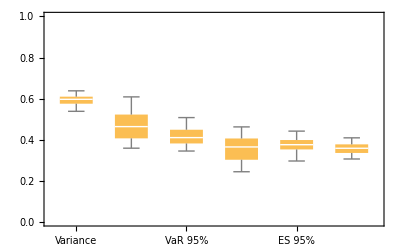

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

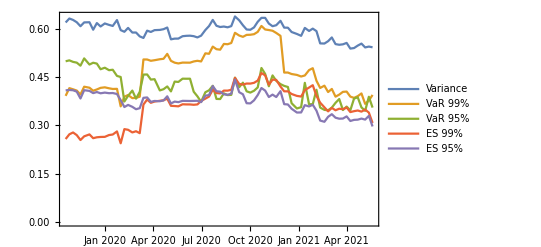

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

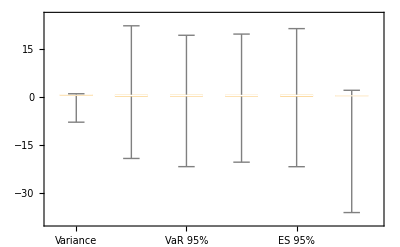

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

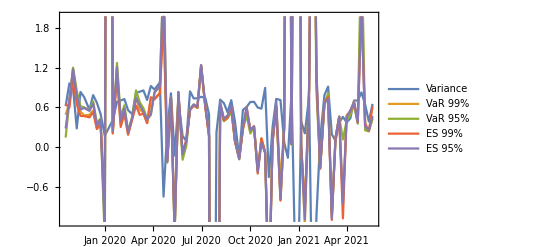

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,8]]
```

log return BITW20

```mathematica
data[[1,7]]
```

log return future

```mathematica
data[[2,2]]
```

2019-10-18 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW20 Price | % Change | log return future | log return BITW20
405 | 2019-10-18 20:00:00+00:00 | 7990. | BTCX19 Curncy | 4851.43 | -2.40% | -0.0142904 | -0.0242449
406 | 2019-10-17 20:00:00+00:00 | 8105. | BTCX19 Curncy | 4970.49 | 4.32% | 0.0142904 | 0.0422964
407 | 2019-10-16 20:00:00+00:00 | 7990. | BTCX19 Curncy | 4764.64 | -4.89% | -0.0295953 | -0.050166
408 | 2019-10-15 20:00:00+00:00 | 8230. | BTCX19 Curncy | 5009.76 | -2.29% | -0.0222298 | -0.0231892
409 | 2019-10-14 20:00:00+00:00 | 8415. | BTCX19 Curncy | 5127.29 | 0.77% | 0. | 0.015811
410 | 2019-10-11 20:00:00+00:00 | 8415. | BTCX19 Curncy | 5046.86 | -1.54% | -0.0275435 | -0.0155164
411 | 2019-10-10 20:00:00+00:00 | 8650. | BTCX19 Curncy | 5125.78 | -1.85% | -0.00403808 | -0.0187031
412 | 2019-10-09 20:00:00+00:00 | 8685. | BTCX19 Curncy | 5222.55 | 5.42% | 0.0544191 | 0.0527683
413 | 2019-10-08 20:00:00+00:00 | 8225. | BTCX19 Curncy | 4954.11 | 0.91% | -0.00787167 | 0.00906376)

```mathematica
hvec
```

{{2019-10-18},{0.868542},{0.719145},{0.888521},{0.637564},{0.820983},{0.88766},{{0.10828405361592813, {h$647602738 -> 0.7191454084602235}},{0.052920584543533836, {h$647602738 -> 0.8885208284507005}},{0.14513846363103747, {h$647602738 -> 0.6375637544794548}},{0.08736640503845719, {h$647602738 -> 0.8209830831720025}},{0.04557099142970885, {h$647602738 -> 0.8876599942302222}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

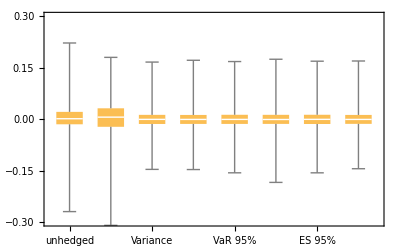

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

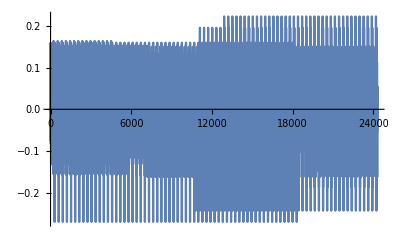

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

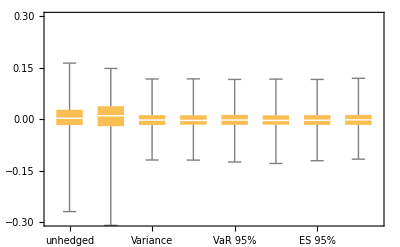

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

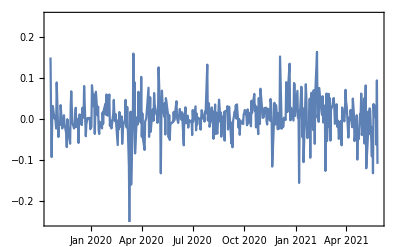
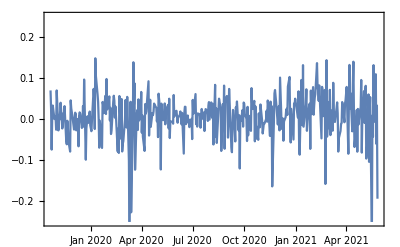

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

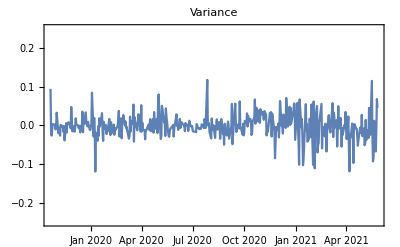
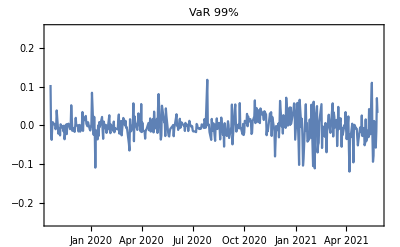
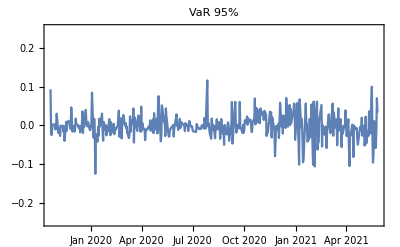
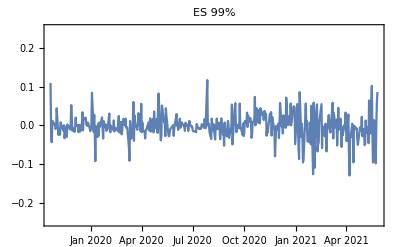
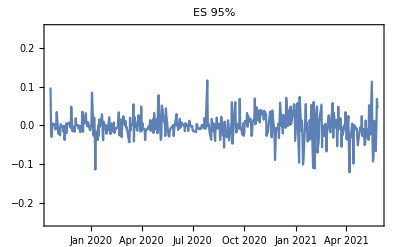
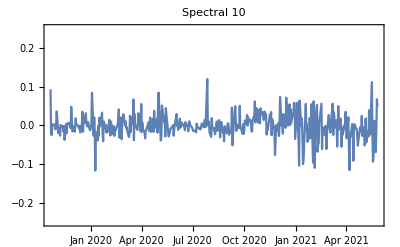

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

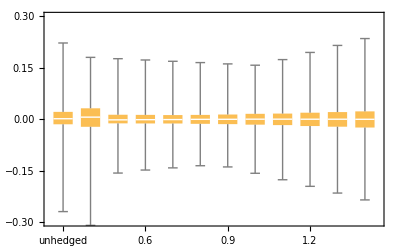

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

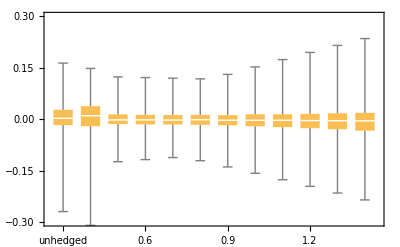

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤80, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.851619 | 0.771181 | 0.778127 | 1.09653 | 0.843499 | 0.864223
2021-05-13 | 0.828097 | 0.806501 | 0.761191 | 0.770782 | 0.819813 | 0.814394
2021-05-06 | 0.825203 | 0.793038 | 0.731834 | 1.03289 | 0.898995 | 0.762489
2021-04-29 | 0.842057 | 0.82709 | 0.7438 | 0.863511 | 0.86308 | 0.797921
2021-04-22 | 0.840062 | 0.818231 | 0.742613 | 0.773534 | 0.79603 | 0.801166
2021-04-15 | 0.839078 | 0.812633 | 0.745563 | 0.766195 | 0.796245 | 0.838754
2021-04-08 | 0.826052 | 0.816689 | 0.73277 | 0.815668 | 0.834171 | 0.793018
2021-04-01 | 0.829089 | 0.833186 | 0.742065 | 0.894986 | 0.844873 | 0.808433
2021-03-25 | 0.831361 | 0.833082 | 0.736466 | 0.861913 | 0.838437 | 0.816773
2021-03-18 | 0.846779 | 0.823241 | 0.740956 | 0.779763 | 0.81984 | 0.802689
2021-03-11 | 0.842026 | 0.816593 | 0.763617 | 0.783265 | 0.820221 | 0.843101
2021-03-04 | 0.856816 | 0.841816 | 0.820535 | 0.895825 | 0.875663 | 0.800849
2021-02-25 | 0.856028 | 0.831669 | 0.808256 | 0.851432 | 0.869779 | 0.853387
2021-02-18 | 0.839998 | 0.852541 | 0.786452 | 0.838598 | 0.838793 | 0.800474
2021-02-10 | 0.8348 | 0.822723 | 0.778495 | 0.822784 | 0.796181 | 0.853142
2021-02-03 | 0.867177 | 0.868681 | 0.784281 | 0.837295 | 0.875079 | 0.846789
2021-01-27 | 0.874486 | 0.909778 | 0.872935 | 1.14056 | 0.961146 | 0.81209
2021-01-20 | 0.8753 | 0.930778 | 0.890766 | 1.13749 | 0.961146 | 0.825467
2021-01-12 | 0.885067 | 0.892223 | 0.835946 | 0.839449 | 0.875521 | 0.866305
2021-01-05 | 0.875003 | 0.864131 | 0.879925 | 1.11949 | 0.959881 | 0.838826
2020-12-28 | 0.872642 | 0.865722 | 0.874566 | 1.08355 | 0.925544 | 0.827542
2020-12-18 | 0.883186 | 0.901062 | 0.838802 | 1.1032 | 0.950174 | 0.820001
2020-12-11 | 0.903132 | 0.874586 | 0.907937 | 0.861108 | 0.884729 | 0.873705
2020-12-04 | 0.9029 | 0.871871 | 0.8506 | 0.861132 | 0.888374 | 0.928378
2020-11-27 | 0.938813 | 0.934928 | 0.984439 | 0.987322 | 0.981634 | 0.835159
2020-11-19 | 0.923091 | 0.869773 | 0.862382 | 0.864407 | 0.983678 | 0.824312
2020-11-12 | 0.921699 | 0.878946 | 0.992644 | 0.852508 | 0.989477 | 0.818892
2020-11-05 | 0.917185 | 0.89008 | 0.982996 | 0.952821 | 0.980958 | 0.807227
2020-10-29 | 0.935367 | 0.885532 | 0.885286 | 0.867713 | 0.988478 | 0.878481
2020-10-22 | 0.936447 | 0.898865 | 0.887629 | 0.871211 | 0.992926 | 0.873593
2020-10-15 | 0.923837 | 0.876968 | 0.979905 | 1.06012 | 0.978483 | 0.821136
2020-10-08 | 0.897863 | 0.866443 | 0.800178 | 0.987154 | 0.929993 | 0.784464
2020-10-01 | 0.888407 | 0.86429 | 0.736093 | 0.92897 | 0.912652 | 0.809265
2020-09-24 | 0.884203 | 0.861741 | 0.732654 | 0.930317 | 0.91063 | 0.792723
2020-09-17 | 0.894469 | 0.85373 | 0.882221 | 0.843982 | 0.957745 | 0.786299
2020-09-10 | 0.89886 | 0.85901 | 0.990037 | 0.927638 | 0.975356 | 0.768456
2020-09-02 | 0.844055 | 0.823008 | 0.915074 | 0.821304 | 0.904351 | 0.717935
2020-08-26 | 0.791493 | 0.813434 | 0.744175 | 0.83314 | 0.868946 | 0.697128
2020-08-19 | 0.782732 | 0.835601 | 0.784221 | 0.809887 | 0.862862 | 0.680594
2020-08-12 | 0.784013 | 0.828059 | 0.787075 | 0.814785 | 0.865006 | 0.682397
2020-08-05 | 0.782428 | 0.86866 | 0.791485 | 0.829213 | 0.87259 | 0.678057
2020-07-29 | 0.787547 | 0.87533 | 0.807022 | 0.824224 | 0.872241 | 0.697894
2020-07-22 | 0.81504 | 0.803554 | 0.885148 | 0.84063 | 0.885711 | 0.710428
2020-07-15 | 0.783243 | 0.783316 | 0.882626 | 0.767121 | 0.858498 | 0.68372
2020-07-08 | 0.77441 | 0.775878 | 0.796474 | 0.764828 | 0.805605 | 0.72701
2020-06-30 | 0.765435 | 0.752768 | 0.761462 | 0.747665 | 0.743044 | 0.708427
2020-06-23 | 0.761245 | 0.756749 | 0.739619 | 0.745233 | 0.764902 | 0.681159
2020-06-16 | 0.766825 | 0.75274 | 0.766494 | 0.743819 | 0.767296 | 0.692678
2020-06-09 | 0.76766 | 0.751974 | 0.764629 | 0.737893 | 0.743801 | 0.737187
2020-06-02 | 0.769465 | 0.75146 | 0.76962 | 0.738233 | 0.745171 | 0.724022
2020-05-26 | 0.769051 | 0.75229 | 0.764909 | 0.737553 | 0.744711 | 0.730882
2020-05-18 | 0.765015 | 0.747872 | 0.758328 | 0.736559 | 0.75666 | 0.678651
2020-05-11 | 0.767074 | 0.754209 | 0.759874 | 0.73845 | 0.75747 | 0.686327
2020-05-04 | 0.770439 | 0.757093 | 0.720422 | 0.742774 | 0.750299 | 0.736507
2020-04-27 | 0.800897 | 0.782889 | 0.873631 | 0.760144 | 0.835568 | 0.718779
2020-04-20 | 0.798581 | 0.762519 | 0.868359 | 0.751749 | 0.853403 | 0.711153
2020-04-13 | 0.799041 | 0.758177 | 0.862604 | 0.751515 | 0.851503 | 0.711578
2020-04-03 | 0.801779 | 0.759875 | 0.858526 | 0.746706 | 0.855022 | 0.740856
2020-03-27 | 0.802255 | 0.756891 | 0.858593 | 0.746477 | 0.854732 | 0.756704
2020-03-20 | 0.80661 | 0.759554 | 0.874567 | 0.7458 | 0.854859 | 0.751069
2020-03-13 | 0.793778 | 0.770564 | 0.866287 | 0.745521 | 0.7892 | 0.700027
2020-03-06 | 0.783012 | 0.651151 | 0.798574 | 0.559633 | 0.726174 | 0.828104
2020-02-28 | 0.793196 | 0.7559 | 0.872833 | 0.638587 | 0.756369 | 0.791942
2020-02-21 | 0.789005 | 0.642473 | 0.79481 | 0.59093 | 0.729507 | 0.836638
2020-02-13 | 0.791334 | 0.669412 | 0.801194 | 0.618534 | 0.744075 | 0.842535
2020-02-06 | 0.787128 | 0.651357 | 0.752401 | 0.60125 | 0.693307 | 0.849523
2020-01-30 | 0.792577 | 0.622641 | 0.802213 | 0.542759 | 0.708754 | 0.832576
2020-01-23 | 0.818731 | 0.79163 | 0.851338 | 0.741387 | 0.81389 | 0.786396
2020-01-15 | 0.802393 | 0.65391 | 0.785926 | 0.638113 | 0.755955 | 0.823068
2020-01-08 | 0.78852 | 0.732947 | 0.821349 | 0.637438 | 0.759263 | 0.774962
2019-12-31 | 0.794982 | 0.738694 | 0.834069 | 0.633218 | 0.772181 | 0.765323
2019-12-23 | 0.789308 | 0.725207 | 0.792598 | 0.62259 | 0.762962 | 0.776658
2019-12-16 | 0.794656 | 0.696023 | 0.867078 | 0.645605 | 0.772796 | 0.772144
2019-12-09 | 0.782831 | 0.632694 | 0.790364 | 0.605845 | 0.752218 | 0.802261
2019-12-02 | 0.801591 | 0.69327 | 0.87184 | 0.64006 | 0.77831 | 0.79523
2019-11-22 | 0.805956 | 0.633456 | 0.852584 | 0.619856 | 0.782719 | 0.79683
2019-11-15 | 0.800896 | 0.729973 | 0.87207 | 0.611046 | 0.783671 | 0.769017
2019-11-08 | 0.812962 | 0.730305 | 0.850296 | 0.649066 | 0.779467 | 0.77656
2019-11-01 | 0.825776 | 0.784631 | 0.869695 | 0.667053 | 0.779916 | 0.830345
2019-10-25 | 0.833107 | 0.748636 | 0.871854 | 0.668409 | 0.807926 | 0.78623
2019-10-18 | 0.868542 | 0.719145 | 0.888521 | 0.637564 | 0.820983 | 0.88766)

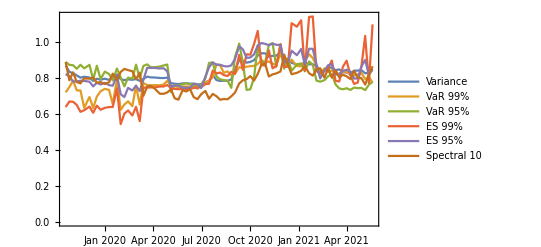

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```